```mathematica
ClearAll["Global`*"];
F = {Q[x],α*Q[x]^2/A[x] + β[x]/(3*ρ*A0[x])*A[x]^(3/2)};F=Simplify[F];
B = {0,KR*Q[x]/A[x] + A[x]/(A0[x]*ρ)*(2/3*A[x]^(1/2)-A0[x]^(1/2))*β'[x]-β[x]/ρ*A[x]/A0[x]^2*(2/3*A[x]^(1/2)-1/2*A0[x]^(1/2))*A0'[x]};B=Simplify[B];
B = {0,-KR*Q[x]/A[x]};
H = { {0,1},{-α*Q[x]^2/A[x]^2+β/(2*ρ*A0[x])*A[x]^(1/2),2*α*Q[x]/A[x]}};H=Simplify[H];
BU = { {D[B[[1]],A[x]],D[B[[1]],Q[x]]},{D[B[[2]],A[x]],D[B[[2]],Q[x]]} };
BU=Simplify[BU];
FLW = F+Δt/2*H.B;FLW=Simplify[FLW];
BLW = B + Δt/2*BU.B;BLW=Simplify[BLW];
FLW[[1]];
FLW[[2]];
F = {Q, Q^2/A + β/(3*ρ) * A^(3/2)};
FU = { {D[F[[1]],A], D[F[[1]],Q]},{D[F[[2]],A], D[F[[2]],Q]}};
p = β*(A*(1/2) - A0^(1/2));
D[p,A]
```

β/2

(x^2-4 x (1+x))/(2 (1+x)^(3/2))+(√(2+x^2) (-x^2+2 x (1+x)))/(1+x)^2-(0.879646 Sin[x])/((2+x^2)^2)

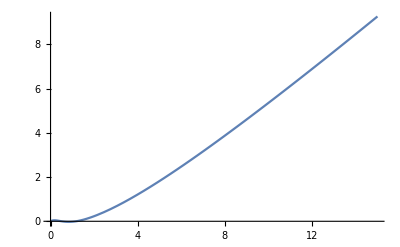

```mathematica
A0[x] = x+1;
A0'[x] = D[A0[x],x];
β[x] = x^2;
β'[x] = D[β[x],x];
A[x]=x^2+2;
Q[x] = Sin[x];
ρ=1;
α=1;
ν = 0.035;
KR = 8*ν*Pi;
dt = 0.00025025025025025025;
BU1 = -KR*Q[x]/A[x]^2 + (β[x] Derivative[1][A0][x]-2 A0[x] Derivative[1][β][x])/(2 ρ A0[x]^(3/2))+(Sqrt[A[x]] (-β[x] Derivative[1][A0][x]+A0[x] Derivative[1][β][x]))/(ρ A0[x]^2)
BU2 = BU[[2,2]];
Plot[BU1,{x,0,15},PlotRange->All]
```